```mathematica
Clear[sol,θ,ω,t];
sol=Block[{c=0.1 ,ρ=2.5},Reap[NDSolve[{θ'[t]==ω[t],ω'[t]==-c ω[t]-Sin[θ[t]]+ρ Sin[t],θ[0]==1.0,ω[0]==1.0,WhenEvent[Mod[t,2 π]==0,Sow[{ArcTan[Sin[θ[t]]/Cos[θ[t]]],ω[t]}]]},{},{t,0.,100000.},MaxSteps->∞]]][[-1,1]];
```

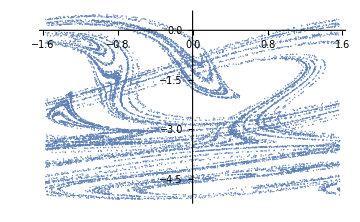

```mathematica
ListPlot[sol,ImageSize->Medium,PlotRange->{{- Pi/2, Pi/2},All},PlotStyle->PointSize[0.0025]]
```

```mathematica
data=Block[{δ=0.15,γ=0.3},Reap[NDSolve[{x''[t]+δ x'[t]-x[t]+x[t]^3==γ Cos[t],x[0]==0,x'[0]==0,WhenEvent[Mod[t,2 π]==0,Sow[{x[t],x'[t]}]]},{},{t,0,100000},MaxSteps->∞]]][[-1,1]];
```

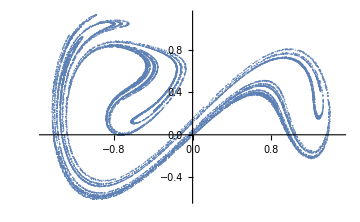

```mathematica
ListPlot[data,ImageSize->Medium,PlotRange->{{-1.5,1.5},All},PlotStyle->PointSize[0.0025]]
```

```mathematica
Clear[θ,ω,sol2,t]
```

```mathematica
c=0.1;ρ=2.5;
```

```mathematica
sol2=NDSolve[{θ'[t]==ω[t],ω'[t]==-c ω[t]-Sin[θ[t]]+ρ Sin[t],θ[0]==1.0,ω[0]==1.0},{θ,ω},{t,0.,50000.}]
```

{{θ→InterpolatingFunction[{{0., 50000.}}, <>],ω→InterpolatingFunction[{{0., 50000.}}, <>]}}

```mathematica
arr=Table[{i,ArcTan[Sin[θ[i]/.sol2[[1,1]]]/Cos[θ[i]/.sol2[[1,1]]]]},{i,0,100,0.01}];
```

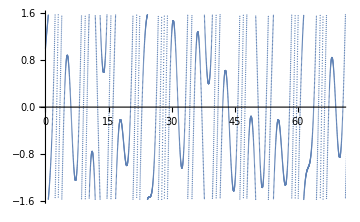

```mathematica
ListPlot[arr,ImageSize->Medium,PlotRange->{{0,70.},All},PlotStyle->PointSize[0.0025]]
```

```mathematica
arr2=Table[{ArcTan[Sin[θ[i]/.sol2[[1,1]]]/Cos[θ[i]/.sol2[[1,1]]],ω[i]/.sol2[[1,2]]]},{i,0,50000,2*Pi}]
```